```mathematica
Clear["Global`*"];
```

```mathematica
$Version
```

12.0.0 for Linux x86 (64-bit) (April 7, 2019)

### Required PDF sets:

For this notebook to run, it requires the following PDF sets;

LHA SETS: {nCTEQ15_208,nCTEQ15np_208,nCTEQ15FullNuc_208_82,nCTEQ15npFullNuc_208_82,nCTEQ15np_1,nCTEQ15_1}
PDS SETS:  {nCTEQ15-p-1,nCTEQ15-np-1,nCTEQ-Pb-208,nCTEQnp-Pb-208}

# Manual file for ManeParse Package Version 5.0

### Version 23.0 18 October 2019 Comments and questions to: Fred Olness olness@physics.smu.edu

## Set Absolute Directory Paths Here

Here we set up all the main directories.
  The rest of the notebook uses only RELATIVE paths.
  We’ll show what goes in each directory below.

```mathematica
(* This just drops the leading path info to make the list of files easier to read *)
(* dropPath=Take[(FileNameSplit /@ # ) //Transpose,-1][[1]]&; *)
dropPath=((Take[#,-1]& /@ (FileNameSplit /@ # )) //Flatten)&
```

Flatten[(Take[#1,-1]&)/@FileNameSplit/@#1]&

```mathematica
(* Remove files that start with "/.*"   
These are the pre-modified CTEQ PDS files and should not be used.  *)
Clear[noDot]
noDot[list_]:=Select[list,!StringMatchQ[#,"*/.*"]&]
```

```mathematica
(* This is where the main notebook file resides *)
workDir=NotebookDirectory[];
FileNames["*",workDir] //dropPath
```

{CalculateRgCTEQ1.nb,CalculateRgCTEQ2.nb,CalculateRgCTEQ.nb,CTEQ15_fafb.png,JetCross1.nb,JetCross.nb,ManeParse_v2.pdf,manual_v5.nb,MP_packages,PDFDIR,README,RgdownvspTCTEQ.dat,RgmidvspTCTEQ.dat,RgupvspTCTEQ.dat,test.nb}

```mathematica
(* This is where the ManeParse files reside *)
dirPackages=workDir<>"/MP_packages";
FileNames["*.m",dirPackages] //dropPath
```

{pdfCalc.m,pdfErrors.m,pdfParseCTEQ.m,pdfParseLHA.m}

```mathematica
(* This is where the LHAPDF files are located *)
(*lhaDir="/usr/local/share/LHAPDF";*)
lhaDir=workDir<>"/PDFDIR/LHA";
Select[FileNames["*",lhaDir],DirectoryQ]  //dropPath
```

{CT10,MSTW2008lo68cl,nCTEQ15_1,nCTEQ15_108,nCTEQ15_119,nCTEQ15_12,nCTEQ15_131,nCTEQ15_14,nCTEQ15_184,nCTEQ15_197,nCTEQ15_20,nCTEQ15_207,nCTEQ15_208,nCTEQ15_27,nCTEQ15_3,nCTEQ15_4,nCTEQ15_40,nCTEQ15_56,nCTEQ15_6,nCTEQ15_64,nCTEQ15_7,nCTEQ15_84,nCTEQ15_9,nCTEQ15FullNuc_108_54,nCTEQ15FullNuc_1_1,nCTEQ15FullNuc_119_59,nCTEQ15FullNuc_12_6,nCTEQ15FullNuc_131_54,nCTEQ15FullNuc_14_7,nCTEQ15FullNuc_184_74,nCTEQ15FullNuc_197_79,nCTEQ15FullNuc_197_98,nCTEQ15FullNuc_20_10,nCTEQ15FullNuc_207_103,nCTEQ15FullNuc_208_82,nCTEQ15FullNuc_27_13,nCTEQ15FullNuc_3_2,nCTEQ15FullNuc_40_18,nCTEQ15FullNuc_40_20,nCTEQ15FullNuc_4_2,nCTEQ15FullNuc_56_26,nCTEQ15FullNuc_6_3,nCTEQ15FullNuc_64_32,nCTEQ15FullNuc_7_3,nCTEQ15FullNuc_84_42,nCTEQ15FullNuc_9_4,nCTEQ15np_1,nCTEQ15np_108,nCTEQ15np_119,nCTEQ15np_12,nCTEQ15np_131,nCTEQ15np_14,nCTEQ15np_184,nCTEQ15np_197,nCTEQ15np_20,nCTEQ15np_207,nCTEQ15np_208,nCTEQ15np_27,nCTEQ15np_3,nCTEQ15np_4,nCTEQ15np_40,nCTEQ15np_56,nCTEQ15np_6,nCTEQ15np_64,nCTEQ15np_7,nCTEQ15np_84,nCTEQ15np_9,nCTEQ15npFullNuc_108_54,nCTEQ15npFullNuc_1_1,nCTEQ15npFullNuc_119_59,nCTEQ15npFullNuc_12_6,nCTEQ15npFullNuc_131_54,nCTEQ15npFullNuc_14_7,nCTEQ15npFullNuc_184_74,nCTEQ15npFullNuc_197_79,nCTEQ15npFullNuc_197_98,nCTEQ15npFullNuc_20_10,nCTEQ15npFullNuc_207_103,nCTEQ15npFullNuc_208_82,nCTEQ15npFullNuc_27_13,nCTEQ15npFullNuc_3_2,nCTEQ15npFullNuc_40_18,nCTEQ15npFullNuc_40_20,nCTEQ15npFullNuc_4_2,nCTEQ15npFullNuc_56_26,nCTEQ15npFullNuc_6_3,nCTEQ15npFullNuc_64_32,nCTEQ15npFullNuc_7_3,nCTEQ15npFullNuc_84_42,nCTEQ15npFullNuc_9_4,NNPDF30_nlo_as_0118}

```mathematica
(* This is where the PDS format files are located *)
pdsDir=workDir<>"/PDFDIR/PDS";
Select[FileNames["*",pdsDir],DirectoryQ]  //dropPath
```

{ct10.pds,ctq66m.pds,nCTEQ15-Ag-108,nCTEQ15-Al-27,nCTEQ15-Ar-40,nCTEQ15-Au-197,nCTEQ15-Be-9,nCTEQ15-C-12,nCTEQ15-Ca-40,nCTEQ15-Cu-64,nCTEQ15-Fe-56,nCTEQ15-He-3,nCTEQ15-He-4,nCTEQ15-Kr-84,nCTEQ15-Li-6,nCTEQ15-Li-7,nCTEQ15-N-14,nCTEQ15-Ne-20,nCTEQ15-p-1,nCTEQ15-Pb-207,nCTEQ15-Pb-208,nCTEQ15-Sn-119,nCTEQ15-W-184,nCTEQ15-Xe-131,nCTEQnp-Ag-108,nCTEQnp-Al-27,nCTEQnp-Ar-40,nCTEQnp-Au-197,nCTEQnp-Be-9,nCTEQnp-C-12,nCTEQnp-Ca-40,nCTEQnp-Cu-64,nCTEQnp-Fe-56,nCTEQnp-He-3,nCTEQnp-He-4,nCTEQnp-Kr-84,nCTEQnp-Li-6,nCTEQnp-Li-7,nCTEQnp-N-14,nCTEQnp-Ne-20,nCTEQnp-p-1,nCTEQnp-Pb-207,nCTEQnp-Pb-208,nCTEQnp-Sn-119,nCTEQnp-W-184,nCTEQnp-Xe-131}

### Required PDF sets:

For this notebook to run, it requires the following PDF sets;
LHA SETS: {CT10,MSTW2008lo68cl,NNPDF30_nlo_as_0118}
PDS SETS:  {ct10.pds,ctq66m.pds}

## Just step through and demo each function:

## Load the packages

#### Loading the main package provides many useful functions

```mathematica
Get[dirPackages<>"/pdfParseLHA.m"]
```

Version: pdfCalc 5.0

Version: ManeParse 5.0: April 2021

- Required Package: pdfCalc --Loaded -

===============================================================

- pdfParseLHA -

Version:  5.0: April 2021

Authors: E.J. Godat, D.B. Clark & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

```mathematica
Get[dirPackages<>"/pdfParseCTEQ.m"]
```

===============================================================

- pdfParseCTEQ -

Version:  5.0:  April 2021

Authors: D.B. Clark, E.J. Godat & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

### pdfCalc.m is already loaded automatically by pdfParseLHA and pdfParseCTEQ, but it won' t hurt to do it again; just ignore the warnings

```mathematica
(* pdfCalc.m is already loaded automatically by pdfParseLHA and pdfParseCTEQ, 
but it won' t hurt to do it again; just ignore the warnings *)

 Get[dirPackages<>"/pdfCalc.m"]
```

Version: pdfCalc 5.0

Version: ManeParse 5.0: April 2021

- Required Package: pdfCalc --Loaded -

SetDelayed::write: Tag pdfReset in pdfReset[] is Protected.

SetDelayed::write: Tag pdfSetListDisplay in pdfSetListDisplay[] is Protected.

SetDelayed::write: Tag pdfSetInterpolator in pdfSetInterpolator[key_:MMA] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

```mathematica
Get[dirPackages<>"/pdfErrors.m"]
```

===============================================================

- pdfErrors -

Version:  5.0; April 2021

Authors: D.B. Clark, E.J. Godat & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

## Set Interpolator

```mathematica
?pdfSetInterpolator
```

```mathematica
pdfSetInterpolator["MMA"]
```

Default Mathematica interpolator will be used.

```mathematica
pdfSetInterpolator["ManeParse"]
```

ManeParse cubic interpolation will be used.

The x-power of the interpolation is set to 1

```mathematica
?pdfSetXpower
```

```mathematica
pdfSetXpower[]
```

ManeParse cubic interpolation will be used.

The x-power of the interpolation is set to 1

```mathematica
pdfSetXpower[2]
```

ManeParse cubic interpolation will be used.

The x-power of the interpolation is set to 2

```mathematica
pdfSetInterpolator["MMA"]
```

Default Mathematica interpolator will be used.

```mathematica
pdfSetXpower[1.5]
```

ManeParse cubic interpolation will be used.

The x-power of the interpolation is set to 1.5

```mathematica
pdfSetInterpolator["MMA"]
```

Default Mathematica interpolator will be used.

## pdfReset

```mathematica
pdfReset[]
```

Default Mathematica interpolator will be used.

All internal variables have been reset.

## Read Individual LHAPDF files

## Read lhapdf file

```mathematica
lhaList=FileNames["*",lhaDir] //noDot;
(* Remove files that are not directories: i.e., of the form *.*  *)
lhaList=lhaList //Select[#,!StringMatchQ[#,"*.*"]&]& ;
lhaList //dropPath
```

{CT10,MSTW2008lo68cl,nCTEQ15_1,nCTEQ15_108,nCTEQ15_119,nCTEQ15_12,nCTEQ15_131,nCTEQ15_14,nCTEQ15_184,nCTEQ15_197,nCTEQ15_20,nCTEQ15_207,nCTEQ15_208,nCTEQ15_27,nCTEQ15_3,nCTEQ15_4,nCTEQ15_40,nCTEQ15_56,nCTEQ15_6,nCTEQ15_64,nCTEQ15_7,nCTEQ15_84,nCTEQ15_9,nCTEQ15FullNuc_108_54,nCTEQ15FullNuc_1_1,nCTEQ15FullNuc_119_59,nCTEQ15FullNuc_12_6,nCTEQ15FullNuc_131_54,nCTEQ15FullNuc_14_7,nCTEQ15FullNuc_184_74,nCTEQ15FullNuc_197_79,nCTEQ15FullNuc_197_98,nCTEQ15FullNuc_20_10,nCTEQ15FullNuc_207_103,nCTEQ15FullNuc_208_82,nCTEQ15FullNuc_27_13,nCTEQ15FullNuc_3_2,nCTEQ15FullNuc_40_18,nCTEQ15FullNuc_40_20,nCTEQ15FullNuc_4_2,nCTEQ15FullNuc_56_26,nCTEQ15FullNuc_6_3,nCTEQ15FullNuc_64_32,nCTEQ15FullNuc_7_3,nCTEQ15FullNuc_84_42,nCTEQ15FullNuc_9_4,nCTEQ15np_1,nCTEQ15np_108,nCTEQ15np_119,nCTEQ15np_12,nCTEQ15np_131,nCTEQ15np_14,nCTEQ15np_184,nCTEQ15np_197,nCTEQ15np_20,nCTEQ15np_207,nCTEQ15np_208,nCTEQ15np_27,nCTEQ15np_3,nCTEQ15np_4,nCTEQ15np_40,nCTEQ15np_56,nCTEQ15np_6,nCTEQ15np_64,nCTEQ15np_7,nCTEQ15np_84,nCTEQ15np_9,nCTEQ15npFullNuc_108_54,nCTEQ15npFullNuc_1_1,nCTEQ15npFullNuc_119_59,nCTEQ15npFullNuc_12_6,nCTEQ15npFullNuc_131_54,nCTEQ15npFullNuc_14_7,nCTEQ15npFullNuc_184_74,nCTEQ15npFullNuc_197_79,nCTEQ15npFullNuc_197_98,nCTEQ15npFullNuc_20_10,nCTEQ15npFullNuc_207_103,nCTEQ15npFullNuc_208_82,nCTEQ15npFullNuc_27_13,nCTEQ15npFullNuc_3_2,nCTEQ15npFullNuc_40_18,nCTEQ15npFullNuc_40_20,nCTEQ15npFullNuc_4_2,nCTEQ15npFullNuc_56_26,nCTEQ15npFullNuc_6_3,nCTEQ15npFullNuc_64_32,nCTEQ15npFullNuc_7_3,nCTEQ15npFullNuc_84_42,nCTEQ15npFullNuc_9_4,NNPDF30_nlo_as_0118}

```mathematica
?pdfParseLHA
```

#### Read in First LHA file

```mathematica
(*file=Select[lhaList,StringMatchQ[#,"*CT10nlo"]&]*)
(*file=Select[lhaList,StringMatchQ[#,"*CT10"]&]*)
file=Select[lhaList,StringMatchQ[#,"*nCTEQ15_1"]&]
```

{/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/LHA/nCTEQ15_1}

```mathematica
FileNames["*",file //First] //noDot //dropPath
```

{nCTEQ15_1_0000.dat,nCTEQ15_1.info}

```mathematica
files=FileNames["*",file //First]  //noDot;
files //dropPath //Short
```

{nCTEQ15_1_0000.dat,nCTEQ15_1.info}

```mathematica
info= Select[files, StringMatchQ[#,"*.info"]&] //First
```

/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/LHA/nCTEQ15_1/nCTEQ15_1.info

```mathematica
dat= Select[files,StringMatchQ[#,"*.dat"]&] //First
```

/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/LHA/nCTEQ15_1/nCTEQ15_1_0000.dat

```mathematica
pdfParseLHA[info,dat]
```

Successfully read /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/LHA/nCTEQ15_1/nCTEQ15_1.info.

Successfully read /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/LHA/nCTEQ15_1/nCTEQ15_1_0000.dat.

1

#### Read in Second LHA file

```mathematica
(*file=Select[lhaList,StringMatchQ[#,"*CT10nlo"]&]*)
(*file=Select[lhaList,StringMatchQ[#,"*CT10"]&]*)
file=Select[lhaList,StringMatchQ[#,"*nCTEQ15_208"]&]
```

{/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/LHA/nCTEQ15_208}

```mathematica
FileNames["*",file //First] //noDot //dropPath
```

{nCTEQ15_208_0000.dat,nCTEQ15_208_0001.dat,nCTEQ15_208_0002.dat,nCTEQ15_208_0003.dat,nCTEQ15_208_0004.dat,nCTEQ15_208_0005.dat,nCTEQ15_208_0006.dat,nCTEQ15_208_0007.dat,nCTEQ15_208_0008.dat,nCTEQ15_208_0009.dat,nCTEQ15_208_0010.dat,nCTEQ15_208_0011.dat,nCTEQ15_208_0012.dat,nCTEQ15_208_0013.dat,nCTEQ15_208_0014.dat,nCTEQ15_208_0015.dat,nCTEQ15_208_0016.dat,nCTEQ15_208_0017.dat,nCTEQ15_208_0018.dat,nCTEQ15_208_0019.dat,nCTEQ15_208_0020.dat,nCTEQ15_208_0021.dat,nCTEQ15_208_0022.dat,nCTEQ15_208_0023.dat,nCTEQ15_208_0024.dat,nCTEQ15_208_0025.dat,nCTEQ15_208_0026.dat,nCTEQ15_208_0027.dat,nCTEQ15_208_0028.dat,nCTEQ15_208_0029.dat,nCTEQ15_208_0030.dat,nCTEQ15_208_0031.dat,nCTEQ15_208_0032.dat,nCTEQ15_208.info}

```mathematica
files=FileNames["*",file //First]  //noDot;
files //dropPath //Short
```

{nCTEQ15_208_0000.dat,nCTEQ15_208_0001.dat,«30»,nCTEQ15_208_0032.dat,nCTEQ15_208.info}

```mathematica
info= Select[files, StringMatchQ[#,"*.info"]&] //First
```

/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208.info

```mathematica
dat= Select[files,StringMatchQ[#,"*.dat"]&] //First
```

/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0000.dat

```mathematica
pdfParseLHA[info,dat]
```

Successfully read /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208.info.

Successfully read /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0000.dat.

2

## Read Individual PDS files

## Read PDS files

```mathematica
pdsList=FileNames["*",pdsDir];
pdsList //dropPath
```

{ct10.pds,ctq66m.pds,nCTEQ15-Ag-108,nCTEQ15-Al-27,nCTEQ15-Ar-40,nCTEQ15-Au-197,nCTEQ15-Be-9,nCTEQ15-C-12,nCTEQ15-Ca-40,nCTEQ15-Cu-64,nCTEQ15-Fe-56,nCTEQ15-He-3,nCTEQ15-He-4,nCTEQ15-Kr-84,nCTEQ15-Li-6,nCTEQ15-Li-7,nCTEQ15-N-14,nCTEQ15-Ne-20,nCTEQ15np.tar.gz,nCTEQ15-p-1,nCTEQ15-Pb-207,nCTEQ15-Pb-208,nCTEQ15-Sn-119,nCTEQ15.tar.gz,nCTEQ15-W-184,nCTEQ15-Xe-131,nCTEQnp-Ag-108,nCTEQnp-Al-27,nCTEQnp-Ar-40,nCTEQnp-Au-197,nCTEQnp-Be-9,nCTEQnp-C-12,nCTEQnp-Ca-40,nCTEQnp-Cu-64,nCTEQnp-Fe-56,nCTEQnp-He-3,nCTEQnp-He-4,nCTEQnp-Kr-84,nCTEQnp-Li-6,nCTEQnp-Li-7,nCTEQnp-N-14,nCTEQnp-Ne-20,nCTEQnp-p-1,nCTEQnp-Pb-207,nCTEQnp-Pb-208,nCTEQnp-Sn-119,nCTEQnp-W-184,nCTEQnp-Xe-131}

```mathematica
?pdfParseCTEQ
```

#### Read in First PDS file

```mathematica
(*"ct10.pds" is a directory of pds files*)
```

```mathematica
(*file=Select[pdsList,StringMatchQ[#,"*ct10.pds"]&]*)
file=Select[pdsList,StringMatchQ[#,"*nCTEQ15-p-1"]&]
files=FileNames["*",file //First]  //noDot;
files //dropPath //Short
```

{/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/PDS/nCTEQ15-p-1}

{nCTEQ15_e00_1_1.pds}

```mathematica
pdfParseCTEQ[files //First]
```

PDF Table for Fit #: ../../results/nCTEQ15/pds-files/nCTEQ15_e00_2_1

3

#### Read in Second PDS file

```mathematica
(*file=Select[pdsList,StringMatchQ[#,"*ctq66m.pds"]&]*)
file=Select[pdsList,StringMatchQ[#,"*nCTEQ15-Pb-208"]&]
files=FileNames["*",file //First]  //noDot;
files //dropPath //Short
```

{/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/PDS/nCTEQ15-Pb-208}

{nCTEQ15_e00_208.pds,nCTEQ15_e01_208.pds,«29»,nCTEQ15_e31_208.pds,nCTEQ15_e32_208.pds}

```mathematica
pdfParseCTEQ[files //First]
```

PDF Table for Fit #: ../../results/nCTEQ15/pds-files/nCTEQ15_e00_208_82

4

## Current PDFs

```mathematica
pdfSetListDisplay[]
```

Set Number | File Name | Max Flavors | Valance Flavors
1 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/LHA/nCTEQ15_1/nCTEQ15_1_0000.dat | 5 | n/a
2 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0000.dat | 5 | n/a
3 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/PDS/nCTEQ15-p-1/nCTEQ15_e00_1_1.pds | 5 | 3
4 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e00_208.pds | 5 | 3

```mathematica
isetMax=Length[pdfSetList]
```

4

```mathematica
Table[{iSet,pdfFunction[iSet,0,0.1,10.]},{iSet,1,isetMax}] //TableForm
```

1 | 10.8134
2 | 13.7648
3 | 10.8134
4 | 13.7648

## PDF short-hand:

## We save the short name "pdf" for a user defined function. If you wish, you can put in some error checking or impose boundaries or positivity here.

```mathematica
pdf[args___]:=pdfFunction[args]
SetAttributes[pdf,Listable];
```

```mathematica
Range[isetMax]
```

{1,2,3,4}

```mathematica
pdf[Range[isetMax],0,0.1,10.]//TableForm
```

10.8134
13.7648
10.8134
13.7648

```mathematica
pdfPositive[args__]:=Module[{},
tmp=pdf[args];
tmp=Max[tmp,0.0];
Return[tmp];
]

{pdf[1,0,0.9,2.0],pdfPositive[1,0,0.9,2.0]}
```

{0.000487792,0.000487792}

## pdfReset

```mathematica
pdfReset[]
```

Default Mathematica interpolator will be used.

All internal variables have been reset.

## Read Groups of LHAPDF files

```mathematica
?pdfFamilyParseLHA
```

#### Read in First LHA file group

```mathematica
(*file=Select[lhaList,StringMatchQ[#,"*CT10nlo"]&]*)
(*file=Select[lhaList,StringMatchQ[#,"*CT10"]&]*)
file=Select[lhaList,StringMatchQ[#,"*nCTEQ15_1"]&]
```

{/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/LHA/nCTEQ15_1}

```mathematica
plha=pdfFamilyParseLHA[file //First]
```

Successfully read /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_1/nCTEQ15_1.info.

Included 1 files in the PDF family.

{1}

#### Read in Second LHA file group

```mathematica
(*file=Select[lhaList,StringMatchQ[#,"*MSTW2008lo68cl"]&]*)
file=Select[lhaList,StringMatchQ[#,"*nCTEQ15_208"]&]
```

{/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/LHA/nCTEQ15_208}

```mathematica
Pblha=pdfFamilyParseLHA[file //First]
```

Successfully read /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208.info.

Included 33 files in the PDF family.

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34}

## Read Groups of PDS files

```mathematica
?pdfFamilyParseCTEQ
```

#### Read in First PDS file group

```mathematica
(*file=Select[pdsList,StringMatchQ[#,"*ct10.pds"]&]*)
file=Select[pdsList,StringMatchQ[#,"*nCTEQ15-p-1"]&]
```

{/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/PDS/nCTEQ15-p-1}

```mathematica
ppds=pdfFamilyParseCTEQ[file //First]
```

Included 1 files in the PDF family.

{35}

#### Read in Second PDS file group

```mathematica
file=Select[pdsList,StringMatchQ[#,"*nCTEQ15-Pb-208"]&]
```

{/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo//PDFDIR/PDS/nCTEQ15-Pb-208}

```mathematica
Pbpds=pdfFamilyParseCTEQ[file //First]
```

Included 33 files in the PDF family.

{36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68}

## Current PDFs

```mathematica
pdfSetListDisplay[]
```

Set Number | File Name | Max Flavors | Valance Flavors
1 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_1/nCTEQ15_1_0000.dat | 5 | n/a
2 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0000.dat | 5 | n/a
3 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0001.dat | 5 | n/a
4 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0002.dat | 5 | n/a
5 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0003.dat | 5 | n/a
6 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0004.dat | 5 | n/a
7 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0005.dat | 5 | n/a
8 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0006.dat | 5 | n/a
9 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0007.dat | 5 | n/a
10 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0008.dat | 5 | n/a
11 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0009.dat | 5 | n/a
12 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0010.dat | 5 | n/a
13 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0011.dat | 5 | n/a
14 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0012.dat | 5 | n/a
15 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0013.dat | 5 | n/a
16 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0014.dat | 5 | n/a
17 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0015.dat | 5 | n/a
18 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0016.dat | 5 | n/a
19 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0017.dat | 5 | n/a
20 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0018.dat | 5 | n/a
21 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0019.dat | 5 | n/a
22 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0020.dat | 5 | n/a
23 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0021.dat | 5 | n/a
24 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0022.dat | 5 | n/a
25 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0023.dat | 5 | n/a
26 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0024.dat | 5 | n/a
27 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0025.dat | 5 | n/a
28 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0026.dat | 5 | n/a
29 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0027.dat | 5 | n/a
30 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0028.dat | 5 | n/a
31 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0029.dat | 5 | n/a
32 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0030.dat | 5 | n/a
33 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0031.dat | 5 | n/a
34 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0032.dat | 5 | n/a
35 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-p-1/nCTEQ15_e00_1_1.pds | 5 | 3
36 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e00_208.pds | 5 | 3
37 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e01_208.pds | 5 | 3
38 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e02_208.pds | 5 | 3
39 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e03_208.pds | 5 | 3
40 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e04_208.pds | 5 | 3
41 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e05_208.pds | 5 | 3
42 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e06_208.pds | 5 | 3
43 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e07_208.pds | 5 | 3
44 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e08_208.pds | 5 | 3
45 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e09_208.pds | 5 | 3
46 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e10_208.pds | 5 | 3
47 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e11_208.pds | 5 | 3
48 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e12_208.pds | 5 | 3
49 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e13_208.pds | 5 | 3
50 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e14_208.pds | 5 | 3
51 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e15_208.pds | 5 | 3
52 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e16_208.pds | 5 | 3
53 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e17_208.pds | 5 | 3
54 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e18_208.pds | 5 | 3
55 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e19_208.pds | 5 | 3
56 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e20_208.pds | 5 | 3
57 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e21_208.pds | 5 | 3
58 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e22_208.pds | 5 | 3
59 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e23_208.pds | 5 | 3
60 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e24_208.pds | 5 | 3
61 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e25_208.pds | 5 | 3
62 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e26_208.pds | 5 | 3
63 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e27_208.pds | 5 | 3
64 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e28_208.pds | 5 | 3
65 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e29_208.pds | 5 | 3
66 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e30_208.pds | 5 | 3
67 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e31_208.pds | 5 | 3
68 | /home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e32_208.pds | 5 | 3

```mathematica
pdfSetList //Short[#,10]&
```

{{1,/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_1/nCTEQ15_1_0000.dat,5,n/a},{2,/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0000.dat,5,n/a},{3,/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/LHA/nCTEQ15_208/nCTEQ15_208_0001.dat,5,n/a},«63»,{67,/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e31_208.pds,5,3},{68,/home/rishi/work/sourendu/ankita/papers/NiharPaper/CTEQ/ManeParse5_Demo/PDFDIR/PDS/nCTEQ15-Pb-208/nCTEQ15_e32_208.pds,5,3}}

```mathematica
isetMax=Length[pdfSetList]
```

68

```mathematica
pdf[Range[isetMax],0,0.1,10.]
```

{10.8134,13.7648,14.5164,12.5641,14.7084,12.4777,13.5225,13.9999,13.3042,13.9678,13.6711,13.8741,13.3718,14.2692,14.0401,12.6974,14.667,13.6902,13.7259,13.8244,12.9277,14.2189,13.9866,13.4646,13.7162,13.3148,13.7023,13.8561,13.3767,14.1388,13.4293,14.1703,13.9969,13.6428,10.8134,13.7648,14.5164,12.5641,14.7084,12.4777,13.5225,13.9999,13.3042,13.9678,13.6711,13.8741,13.3718,14.2692,14.0401,12.6974,14.667,13.6902,13.7259,13.8244,12.9277,14.2189,13.9866,13.4646,13.7162,13.3148,13.7023,13.8561,13.3767,14.1388,13.4293,14.1703,13.9969,13.6428}

## Plot PDFs

```mathematica
q0=100.;
iset0=1;
iParton0=0;
```

```mathematica
fullSetList={ppds,Pbpds,plha,Pblha};
setList=First /@ fullSetList
```

{35,36,1,2}

#### Plot single flavor of multiple PDF

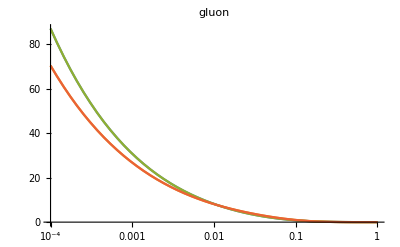

```mathematica
ipart=0;
LogLinearPlot[
Table[ x pdf[setList[[i]],ipart,x,q0],{i,1,Length[setList]}] //Evaluate
,{x,10^-4,1},PlotLabel->pdfFlavor[ipart]]  //Print
```

```mathematica
ipart=0;
i=1;
NIntegrate[pdf[setList[[i]],ipart,x,q0]* pdf[setList[[i]],ipart,x,q0]*1//Evaluate,{x,0.001,1-0.001}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.001812815326759742375235806566280416518566198647022247314453125}. NIntegrate obtained 461673. and 18.0263 for the integral and error estimates.

461673.

## Speed Test: 1000 calls of each set

```mathematica
pdfSetInterpolator["MMA"]
```

Default Mathematica interpolator will be used.

## Error PDF w/ Hessian sets

```mathematica
xlist=Table[10.^i,{i,-4,0,1/8}] //Drop[#,-1]&
```

{0.0001,0.000133352,0.000177828,0.000237137,0.000316228,0.000421697,0.000562341,0.000749894,0.001,0.00133352,0.00177828,0.00237137,0.00316228,0.00421697,0.00562341,0.00749894,0.01,0.0133352,0.0177828,0.0237137,0.0316228,0.0421697,0.0562341,0.0749894,0.1,0.133352,0.177828,0.237137,0.316228,0.421697,0.562341,0.749894}

```mathematica
?pdfHessianError
```

```mathematica
pdf[ppds,0,0.1,10.]
pdfHessianError[pdf[ppds,0,0.1,10.]]
```

{10.8134}

0

```mathematica
pdf[plha,0,0.1,10.]
pdfHessianError[pdf[plha,0,0.1,10.]]
```

{10.8134}

0

```mathematica
pdf[Pbpds,0,0.1,10.]
pdfHessianError[pdf[Pbpds,0,0.1,10.]]
```

{13.7648,14.5164,12.5641,14.7084,12.4777,13.5225,13.9999,13.3042,13.9678,13.6711,13.8741,13.3718,14.2692,14.0401,12.6974,14.667,13.6902,13.7259,13.8244,12.9277,14.2189,13.9866,13.4646,13.7162,13.3148,13.7023,13.8561,13.3767,14.1388,13.4293,14.1703,13.9969,13.6428}

2.02786

```mathematica
pdf[Pblha,0,0.1,10.]
pdfHessianError[pdf[Pblha,0,0.1,10.]]
```

{13.7648,14.5164,12.5641,14.7084,12.4777,13.5225,13.9999,13.3042,13.9678,13.6711,13.8741,13.3718,14.2692,14.0401,12.6974,14.667,13.6902,13.7259,13.8244,12.9277,14.2189,13.9866,13.4646,13.7162,13.3148,13.7023,13.8561,13.3767,14.1388,13.4293,14.1703,13.9969,13.6428}

2.02786

```mathematica
(*Plots with errors and relative errors*)
```

```mathematica
ipart0=0;
q0=10.;
(*Takes a long time*)
(*LogLinearPlot[pdfHessianError[pdf[Pblha,ipart0,x,q0]]/pdf[Pblha[[1]],ipart0,x,q0],{x,10.^-4,0.7}]*)
(*LogLinearPlot[pdfHessianError[pdf[Pbpds,ipart0,x,q0]]/pdf[Pbpds[[1]],ipart0,x,q0],{x,10.^-4,0.7}]*)
```

```mathematica
central=pdf[Pblha[[1]],ipart0,#,q0]& /@ xlist;
(*central≠mean value*)
nsets=Length[Pblha];
meanval=Sum[pdf[Pblha[[i]],ipart0,#,q0]& /@ xlist,{i,1,nsets}]/nsets;
Norm[meanval-central]
error=pdfHessianError[pdf[Pblha,ipart0,#,q0]]& /@ xlist;
Pbcentral=central+0.0;
Pberror=error+0.0;
```

2804.46

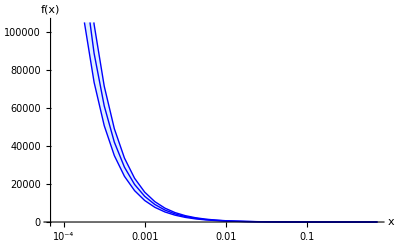

```mathematica
Pbmid=Transpose[{xlist,central}];
Pbup=Transpose[{xlist,central+error}];
Pbdown=Transpose[{xlist,central-error}];
ListLogLinearPlot[ {Pbup,Pbmid,Pbdown},
Joined->True,
Filling->{2},
FillingStyle->LightBlue,
PlotStyle->({#,Blue}& /@  {Thin,Thick,Thin}),AxesLabel->{"x","f(x)"}
]
```

```mathematica
(*Gluon pdfs for protons*)
ipart0=0;
pT=10.0;
q0=pT;
```

```mathematica
central=pdf[plha[[1]],ipart0,#,q0]& /@ xlist;
(*central≠mean value*)
nsets=Length[plha];
meanval=Sum[pdf[plha[[i]],ipart0,#,q0]& /@ xlist,{i,1,nsets}]/nsets;
Norm[meanval-central]
error=pdfHessianError[pdf[plha,ipart0,#,q0]]& /@ xlist;
pcentral=central+0.0;
perror=error+0.0;
```

0.

```mathematica
(*pdferror=0. Why?*)
Norm[perror]
```

0.

{0.0001,0.000133352,0.000177828,0.000237137,0.000316228,0.000421697,0.000562341,0.000749894,0.001,0.00133352,0.00177828,0.00237137,0.00316228,0.00421697,0.00562341,0.00749894,0.01,0.0133352,0.0177828,0.0237137,0.0316228,0.0421697,0.0562341,0.0749894,0.1,0.133352,0.177828,0.237137,0.316228,0.421697,0.562341,0.749894}

{370960.,254537.,174445.,119380.,81572.8,55638.2,37890.3,25752.3,17466.9,11819.6,7978.07,5369.34,3598.86,2401.89,1594.08,1050.8,686.599,443.49,282.217,176.326,107.728,63.9978,36.8209,20.3942,10.8134,5.44323,2.56536,1.10593,0.417748,0.126784,0.0254093,0.00173997}

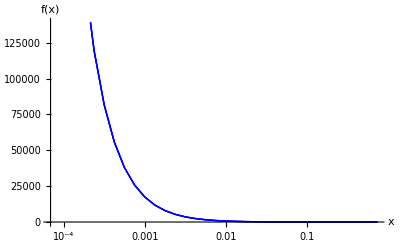

```mathematica
(*ListPlot*)
xlist
central
pmid=Transpose[{xlist,central}];
pup=Transpose[{xlist,central+error}];
pdown=Transpose[{xlist,central-error}];
ListLogLinearPlot[ {pup,pmid,pdown},
Joined->True,
Filling->{2},
FillingStyle->LightBlue,
PlotStyle->({#,Blue}& /@  {Thin,Thick,Thin}),AxesLabel->{"x","f(x)"}
]
```

```mathematica
(*Interpolated PDFs*)
```

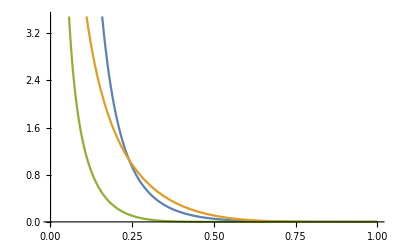

```mathematica
Plot[{pdf[plha[[1]],ipart0,x,q0],pdf[plha[[1]],1,x,q0],pdf[plha[[1]],-1,x,q0]},{x,0.001,1}]
```

```mathematica
(*Sum rules checks*)
```

```mathematica
(*Momentum conservation. We ignore the top quark throughout*)
NIntegrate[x*pdf[plha[[1]],0,x,q0]+x*pdf[plha[[1]],1,x,q0]+x*pdf[plha[[1]],-1,x,q0]+x*pdf[plha[[1]],2,x,q0]+x*pdf[plha[[1]],-2,x,q0]+x*pdf[plha[[1]],3,x,q0]+x*pdf[plha[[1]],-3,x,q0]+x*pdf[plha[[1]],4,x,q0]+x*pdf[plha[[1]],-4,x,q0]+x*pdf[plha[[1]],5,x,q0]+x*pdf[plha[[1]],-5,x,q0],{x,0.0001,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000602919}. NIntegrate obtained 0.992169 and 1.98824×10^-6 for the integral and error estimates.

0.992169

```mathematica
(*b-quark minus antiquark*)
NIntegrate[pdf[plha[[1]],5,x,q0]-pdf[plha[[1]],-5,x,q0],{x,0.0001,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
(*c-quark minus antiquark*)
NIntegrate[pdf[plha[[1]],4,x,q0]-pdf[plha[[1]],-4,x,q0],{x,0.0001,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
(*s-quark minus antiquark*)
NIntegrate[pdf[plha[[1]],3,x,q0]-pdf[plha[[1]],-3,x,q0],{x,0.0001,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
(*d-quark minus antiquark*)
NIntegrate[pdf[plha[[1]],1,x,q0]-pdf[plha[[1]],-1,x,q0],{x,0.0001,1}]
```

0.975018

```mathematica
(*u-quark minus antiquark*)
NIntegrate[pdf[plha[[1]],2,x,q0]-pdf[plha[[1]],-2,x,q0],{x,0.0001,1}]
```

1.97514

```mathematica
(*Importing scattering processes*)
```

```mathematica
x
xx
x4
```

x

xx

x4

```mathematica
(*x and xx as variable names in scatcrossf.m cause conflicts with Global variables in ManeParse. So we use x4 or as the variable name.*)
(*I have assumed that there is no difference between S and s in scatcrossf.m and replaced S->s throughtout. I was getting errors associated with this. Please check this?*)
(*Get["/home/rishi/Dropbox/jets/codes/scatcross.wl"]*)
Get["/home/rishi/Dropbox/jets/codes/scatcrossf.m"]
GTR
v3
```

3/2

40/9

```mathematica
(*Checking NIntegrate syntax for multiple integration*)
NIntegrate[x4,{y,0,x4},{x4,0,1}]
NIntegrate[x4,{x4,0,1},{y,0,x4}]
```

NIntegrate::nlim: y = x4 is not a valid limit of integration.

NIntegrate[x4,{y,0,x4},{x4,0,1}]

0.333333

```mathematica
(*Checking Switch syntax*)
JJ=2;
Switch[JJ,1,ans=1,2,ans=2,_,ans=0];
Print[ans]
JJ=5;
Switch[JJ,1,ans=1,2,ans=2,_,ans=0];
Print[ans]
```

2

0

```mathematica
xbminfn[xa_,V_,Z_]:=Return[((1-V)/(1+(1-V-Z)/xa))];
```

```mathematica
dsigmaab[xa_,xb_,pT_,eta_,zc_,s_,JJ_]:=Block[{v,z,pThat,etahat,shat,ans},shat=xa*xb*s;pThat=pT/zc;etahat=eta-Log[xa/xb]/2;v=1-(2*pThat)/(√shat)*Exp[-etahat];(*Typo in 1606.06732 Eq.4.2??*)z=2*pThat/(√s)*Cosh[etahat];(*Do we need to add Born, LO, and DEL contributions? Here I've only added PL.*)Switch[JJ,1,ans=AvwPL1[z,v,s,pThat],2,ans=AvwPL2[z,v,s,pThat],3,ans=AvwPL3[z,v,s,pThat],4,ans=AvwPL4[z,v,s,pThat],5,ans=AvwPL5[z,v,s,pThat],6,ans=AvwPL6[z,v,s,pThat],7,ans=AvwPL7[z,v,s,pThat],8,ans=AvwPL8[z,v,s,pThat],9,ans=AvwPL9[z,v,s,pThat],10,ans=AvwPL10[z,v,s,pThat],11,ans=AvwPL11[z,v,s,pThat],12,ans=AvwPL12[z,v,s,pThat],13,ans=AvwPL13[z,v,s,pThat],14,ans=AvwPL14[z,v,s,pThat],15,ans=AvwPL15[z,v,s,pThat],16,ans=AvwPL16[z,v,s,pThat],_,0];Return[ans]]
```

```mathematica
dsigma[pT_,eta_,zc_,s_,JJ_]:=Block[{V,Z,xamin,xbmin,ans2,ipart0=0,ipartD=1,ipartDbar=-1,iparta,ipartb,q0},
(*q0=pT. Is this the correct scale? Does this make the NLO correction small? Or should we use pT/zc or v*pT?*)
q0=pT;
V=1-(2*pT)/(√s)*Exp[-eta];(*Typo in 1606.06732 Eq.4.4??*)Z=2*pT/(√s)*Cosh[eta];xamin=1-((1-Z)/V);(*The table needs to be completed?*)Switch[JJ,16,iparta=ipart0;ipartb=ipart0,15,iparta=ipart0;ipartb=ipart0];ans2=NIntegrate[(2*pT)/s*pdf[plha[[1]],iparta,xa,q0]*pdf[plha[[1]],ipartb,xb,q0]*dsigmaab[xa,xb,pT,eta,zc,s,JJ],{xa,xamin,1},{xb,xbminfn[xa,V,Z],1}];Return[ans2]]
```

```mathematica
dsigmaab[0.5,0.5,50,0,0.5,2760.0,16]
```

(-12183.1-12364.7 ⅈ)+65884.8 ((-1.37577+3.14159 ⅈ) CGGL[0.290844]+CGGW[0.290844])+391.236 CGGW[w]+8/3 (-635.532 ((-1.37577+3.14159 ⅈ) CQGL[0.290844]+CQGW[0.290844])+8.52106 CQGW[w])-0.0000633027 ((1.88917+3.14159 ⅈ) (-1.69819×10^6 (-4+CQ)+1.52837×10^7 (-319.371+101.714 CQ))+2.02997 (1.69819×10^6 CQ-1.52837×10^7 (-115.942+101.714 CQ))-3.10574×10^9 Log[S/M^2]-6.90165×10^8 Log[S/MP^2])

```mathematica
dsigma[50,0,0.5,2760.0,16]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.